```mathematica
k1=2;k2=3; At = 100;Bt=80;
```

```mathematica
Cvalues = NDSolveValue[{CC'[t]==k1(At-CC[t])(Bt-CC[t])-k2*CC[t],CC[0]==0},CC,{t,0,.1}];
```

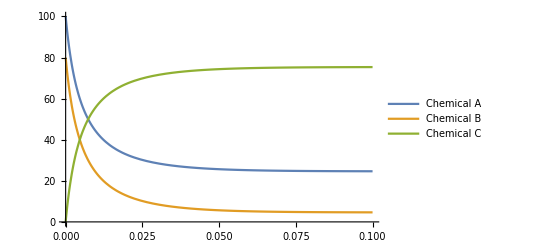

```mathematica
Plot[{100-Cvalues[t],80-Cvalues[t],Cvalues[t]},{t,0,.1},PlotLegends->{"Chemical A","Chemical B","Chemical C"}]
```